## Simulation results: antigenic escape with cross immunity

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sasaki/Dropbox/@Res-SHARED/@OLIGOMORPH/Antigenic Escape and virulence/Antigen Escape and Virulence Evolution/Manusripts/-Source codes for figures/Figure 1

## parameters

```mathematica
σ=Range[0.1,2.0,0.1]
Length[σ]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

20

```mathematica
par={β->2,γ->0.5,α->0.1,u->0.001};
r0=β-(u+γ+α)/.par;
𝒟=0.001;
v=2Sqrt[r0 𝒟]
```

0.0748064

Viewpoint default

```mathematica
vpt={1.5,-.3,0.7}
```

{1.5,-0.3,0.7}

## Bifurcation diagram

```mathematica
Clear[da]
NPARA=20;
Do[
fname="dat/mean-"<>ToString[npara]<>".d";
da[npara] = ReadList[fname,Number,RecordLists->True],
{npara,0,NPARA-1}]
```

```mathematica
da[1]//Length
```

6000

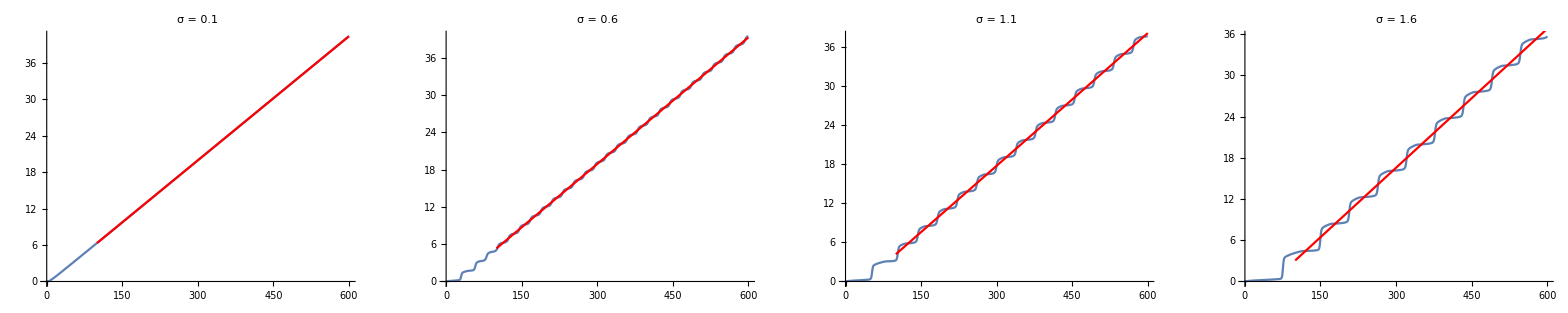

```mathematica
Clear[time,it,ex,vx,t,daa,sig,S,data];
gGrace=1000;
delta={};
speed={};
Do[
daa=da[npara];
{time,it,ex,vx}=Transpose[daa];
sig=σ⟦npara+1⟧;
S=sig/Sqrt[2𝒟/r0]/.par;
data=Take[Transpose[{time,ex}],{gGrace,Length[daa]}];
{timed,exd}=Transpose[data];
lm=Fit[data,{1,t},t];
vsim=Fit[data,{1,t},t,"BestFitParameters"]⟦2⟧;
fitted=lm/.{t->timed};
δsqrt=Sqrt[Total[(exd-fitted)^2]/(Length[daa]-gGrace)];
g[npara+1]=Show[
ListLinePlot[Transpose[{time,ex}]
,PlotLabel->"σ = "<>ToString[sig]],
Plot[lm,{t,Min[timed],Max[timed]}
,PlotStyle->Red]];
AppendTo[delta,{sig,δsqrt}];
AppendTo[speed,{sig,vsim}],
{npara,0,NPARA-1}
]
GraphicsRow[Table[g[1+5i],{i,0,3}]]
```

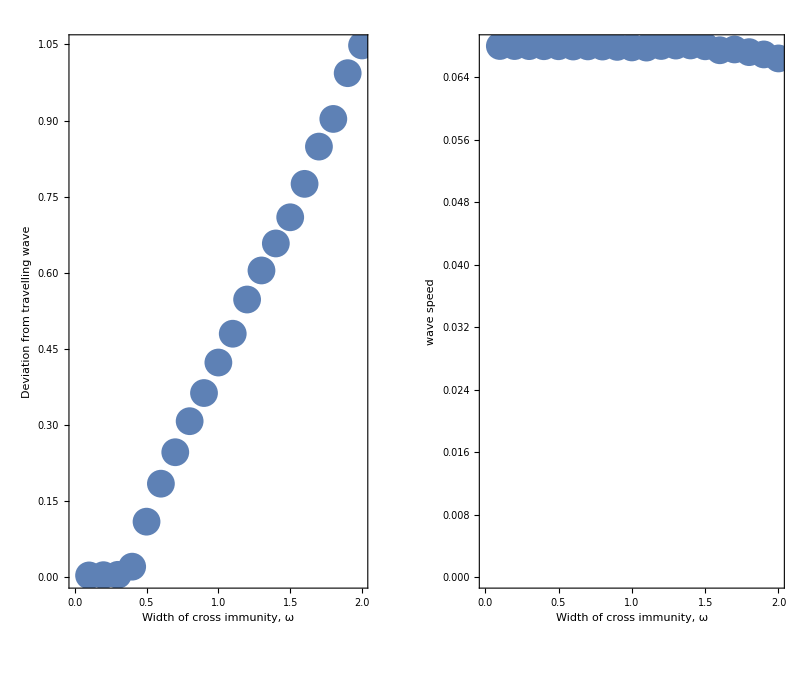

```mathematica
p1=ListPlot[delta,PlotStyle->PointSize[0.05],AspectRatio->2,Frame->True,FrameLabel->{"Width of cross immunity, ω", "Deviation from travelling wave"}];
p2=ListPlot[speed,PlotStyle->PointSize[0.05],AspectRatio->2,Frame->True,FrameLabel->{"Width of cross immunity, ω", "wave speed"},PlotRange->{0,Automatic},Epilog->{Dashed,Line[{{0,v},{2,v}}]}];
GraphicsRow[{p1,p2}]
```